```mathematica
my指数分布=ExponentialDistribution[1/8000]
```

ExponentialDistribution[1/8000]

```mathematica
PDF[my指数分布] (*获得"概率函数"*)
```

Function[x,Piecewise[{{ⅇ^(-x/8000)/8000, x≥0}, {0, True}}],Listable]

```mathematica
CDF[my指数分布](*获得"累加函数"*)
```

Function[x,Piecewise[{{1-ⅇ^(-x/8000), x≥0}, {0, True}}],Listable]

```mathematica
CDF[my指数分布,5000]
```

(在x=5000处的 累加函数F(x)值=0.46)

1-1/ⅇ^(5/8)

```mathematica
N[1-1/ⅇ^(5/8)]
```

0.464739

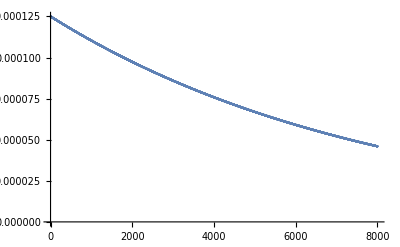

```mathematica
ListPlot[Table[PDF[my指数分布,x],{x,0,8000}],
PlotLegends->"PDF=ⅇ^(-x/8000)/8000"]
```

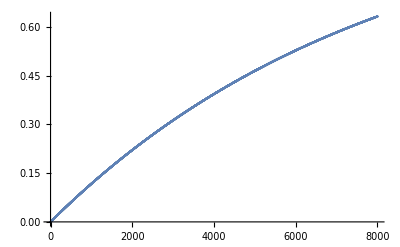

```mathematica
ListPlot[Table[CDF[my指数分布,x],{x,0,8000}],
PlotLegends->"CDF=1-ⅇ^(-x/8000)"]
```